```mathematica
gpd=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-t-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpd;
Her=Query[1,2]@gpd;
Hda=Query[1,3]@gpd;
Edg=Query[2,1]@gpd;
Eer=Query[2,2]@gpd;
Eda=Query[2,3]@gpd;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
gpdg=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-u-up-xi1-pi-noD.wdx"];
Hdg=Query[1,1]@gpdg;
Her=Query[1,2]@gpdg;
Hda=Query[1,3]@gpdg;
Edg=Query[2,1]@gpdg;
Eer=Query[2,2]@gpdg;
Eda=Query[2,3]@gpdg;
Hdgf=Interpolation[Flatten[Hdg,1]];
Herf=Interpolation[Flatten[Her,1]];
Hdaf=Interpolation[Flatten[Hda,1]];
Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];
```

```mathematica
Herall[x_,t_]:=Herf[x,t]+Hdaf[x,t];
Eerall[x_,t_]:=Eerf[x,t]+Edaf[x,t];
```

```mathematica
(*Edgf=Interpolation[Flatten[Edg,1]];
Eerf=Interpolation[Flatten[Eer,1]];
Edaf=Interpolation[Flatten[Eda,1]];*)
```

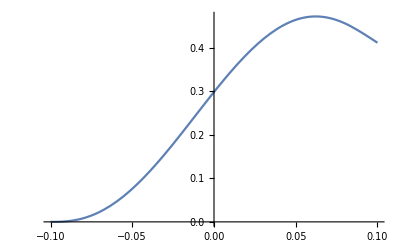

```mathematica
Plot[I*Herf[x,-1],{x,-0.1,0.1}]
```

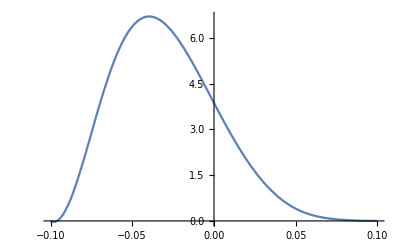

```mathematica
Plot[I*Hdaf[x,-1],{x,-0.1,0.1}]
```

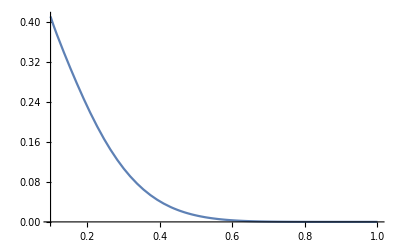

```mathematica
Plot[I*Hdgf[x,-1],{x,0.1,1}]
```

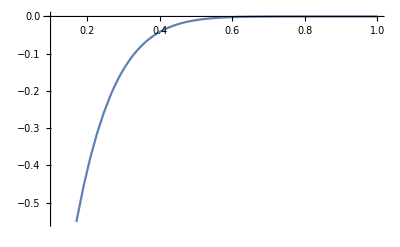

```mathematica
Plot[I*Edgf[x,-1],{x,0.1,1}]
```

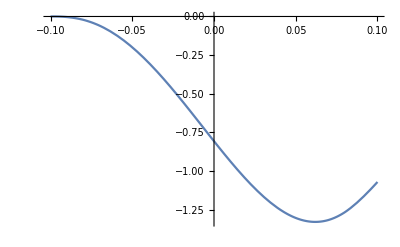

```mathematica
Plot[I*Eerf[x,-1],{x,-0.1,0.1}]
```

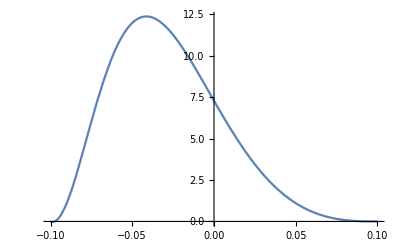

```mathematica
Plot[I*Edaf[x,-1],{x,-0.1,0.1}]
```

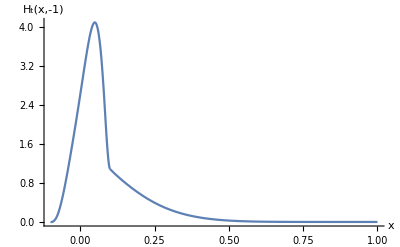

```mathematica
pHt2d=Show[Plot[-I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[-I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_t(x,-1)"}]
```

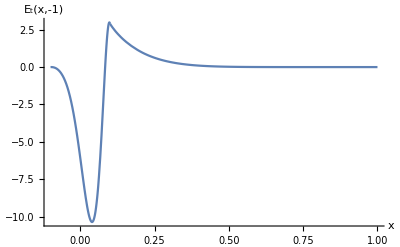

```mathematica
pEt2d=Show[Plot[I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_t(x,-1)"}]
```

```mathematica
Plot3D[-I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-

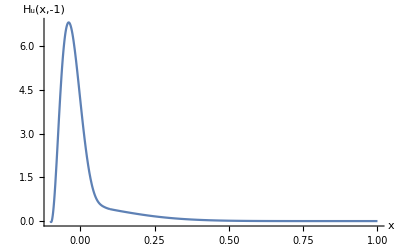

```mathematica
pHu2d=Show[Plot[I*Hdgf[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Herall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","H_u(x,-1)"}]
```

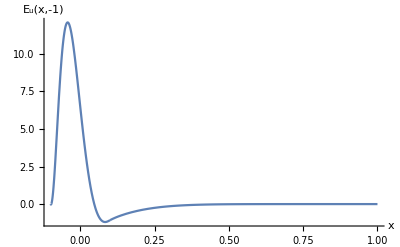

```mathematica
pEu2d=Show[Plot[I*Edgf[x,-1],{x,0.1,1},PlotRange->All],Plot[I*Eerall[x,-1],{x,-0.1,0.1},PlotRange->All],AxesLabel->{"x","E_u(x,-1)"}]
```

```mathematica
pHu3d=Show[Plot3D[I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEu3d=Show[Plot3D[I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_u(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pHt3d=Show[Plot3D[-I*Hdgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Herall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","H_t(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
pEt3d=Show[Plot3D[-I*Edgf[x,t],{x,0.1,1},{t,-1,-0.03562509090909091},PlotRange->All],Plot3D[-I*Eerall[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All],AxesLabel->{"x","t","E_t(x,ξ,t)"},LabelStyle->Directive[Black,Thick,12]]
```

-Graphics3D-

```mathematica
tpathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Hu-0.1.pdf"}];
```

```mathematica
tpathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Eu-0.1.pdf"}];
```

```mathematica
tpathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Eu-0.1-2d.pdf"}];
```

```mathematica
tpathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"t-Hu-0.1-2d.pdf"}];
```

```mathematica
upathH3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Hu-0.1.pdf"}];
upathH=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Hu-0.1-2d.pdf"}];
```

```mathematica
upathE3d=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Eu-0.1.pdf"}];
upathE=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\228test",
"u-Eu-0.1-2d.pdf"}];
```

```mathematica
Export[upathH3d,pHu3d]
Export[upathH,pHu2d]
```

G:\calc-online\gpd\3dre\228test\u-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\u-Hu-0.1-2d.pdf

```mathematica
Export[upathE3d,pEu3d]
Export[upathE,pEu2d]
```

G:\calc-online\gpd\3dre\228test\u-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\u-Eu-0.1-2d.pdf

```mathematica
Export[tpathH3d,pHt3d]
Export[tpathH,pHt2d]
```

G:\calc-online\gpd\3dre\228test\t-Hu-0.1.pdf

G:\calc-online\gpd\3dre\228test\t-Hu-0.1-2d.pdf

```mathematica
Export[tpathE3d,pEt3d]
Export[tpathE,pEt2d]
```

G:\calc-online\gpd\3dre\228test\t-Eu-0.1.pdf

G:\calc-online\gpd\3dre\228test\t-Eu-0.1-2d.pdf

```mathematica
SubscriptBox["H",e]//DisplayForm
```

H_e

```mathematica
Plot3D[Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[-I*Eerf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

InterpolatingFunction::dmval: Input value {-0.0607143,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0589286,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0598214,-0.0356252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics3D-

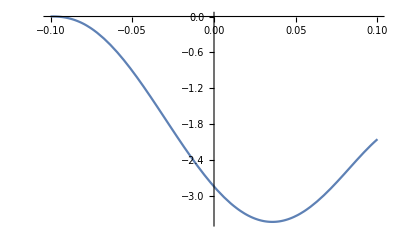

```mathematica
Plot[-I*Chop[Eerf[x,-0.1],10^-9],{x,-0.1,0.1}]
```

```mathematica
Eerf[0,-0.1]
```

0.-2.83547 ⅈ

```mathematica
Eerf[0.02,-0.1]
```

-8.32662×10^-26-3.30567 ⅈ

```mathematica
Eerf[-0.005,-0.1]
```

-1.49999×10^-11-2.67216 ⅈ

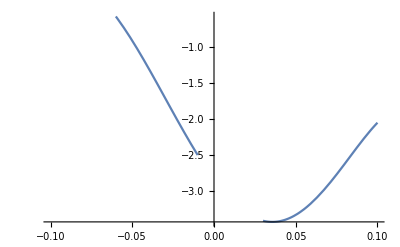

```mathematica
Plot[-I*Eerf[x,-0.1],{x,-0.1,0.1}]
```

```mathematica
Plot3D[I*Herf[x,t],{x,-0.1,0.1},{t,-1,-0.03562509090909091},PlotRange->All]
```

-Graphics3D-